```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

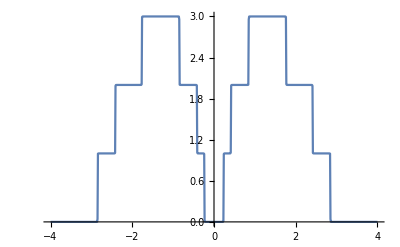

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
(*ρ33:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ34:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ35:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ36:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ33:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ38:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ39:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200];A3:= {{3,3,ρ33},{3,4,ρ34},{3,5,ρ35},{3,6,ρ36},{3,3,ρ33},{3,8,ρ38},{3,9,ρ39}}
ρ43:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ44:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ45:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ46:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ44:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ48:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ49:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A4:= {{4,3,ρ43},{4,4,ρ44},{4,5,ρ45},{4,6,ρ46},{4,4,ρ44},{4,8,ρ48},{4,9,ρ49}}
ρ53:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ54:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ55:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ56:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ55:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ58:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ59:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A5:= {{5,3,ρ53},{5,4,ρ54},{5,5,ρ55},{5,6,ρ56},{5,5,ρ55},{5,8,ρ58},{5,9,ρ59}}
ρ63:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ64:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ65:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ66:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ66:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ68:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ69:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A6:= {{6,3,ρ63},{6,4,ρ64},{6,5,ρ65},{6,6,ρ66},{6,6,ρ66},{6,8,ρ68},{6,9,ρ69}}
ρ73:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ74:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ75:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ76:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ77:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ78:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ79:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A7:= {{7,3,ρ73},{7,4,ρ74},{7,5,ρ75},{7,6,ρ76},{7,7,ρ77},{7,8,ρ78},{7,9,ρ79}}
ρ83:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp3.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ84:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp4.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ85:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ86:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ88:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ88:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp8.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
ρ89:=Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp9.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]
A8:= {{8,3,ρ83},{8,4,ρ84},{8,5,ρ85},{8,6,ρ86},{8,8,ρ88},{8,8,ρ88},{8,9,ρ89}}
A:=Join[A3,A4,A5,A6,A7,A8]
{A[[Position[A,Min[Join[A3,A4,A5,A6,A7,A8]]][[1,1]],1]],A[[Position[A,Min[Join[A3,A4,A5,A6,A7,A8]]][[1,1]],2]],A[[Position[A,Min[Join[A3,A4,A5,A6,A7,A8]]][[1,1]],3]]}*)
```

{3,5,0.000318023}

```mathematica
υ[ϵ1_,τ_]:=Module[{μ1=RandomInteger[{1,7}],μ2=RandomInteger[{1,7}],μ3=RandomInteger[{1,7}],μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}],μ6=RandomInteger[{1,7}],μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}]},
(*Print[{μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8}];*)
η5:=Module[{g:=Inverse[β[ω,0.001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp5.T2[1].Sl15.T2[1]].imp5;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];
Clear[m5];m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];(*
ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)]*);
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8}(*{9,ρ9},{10,ρ10}*)};(*Print[list];*){list[[Position[list,Min[list]][[1,1]],1]],Min[list]}]
```

```mathematica
Timing[υ[0.5,1]]
```

{2.74915,{6,0.000397944}}

```mathematica
f[τ_]:=f[τ]=Table[υ[0.5,τ],50]
```

```mathematica
ϕ[τ_]:=2*(Count[Part[f[τ],;;,1],5]+Count[Part[f[τ],;;,1],7]+Count[Part[f[τ],;;,1],6])/100
```

```mathematica
Table[{τ,ϕ[τ]},{τ,Range[0.1,3,0.1]}]
```

{{0.1,19/50},{0.2,12/25},{0.3,2/5},{0.4,7/10},{0.5,41/50},{0.6,19/25},{0.7,31/50},{0.8,7/10},{0.9,7/10},{1.,27/50},{1.1,27/50},{1.2,37/50},{1.3,39/50},{1.4,7/10},{1.5,7/10},{1.6,37/50},{1.7,37/50},{1.8,4/5},{1.9,41/50},{2.,21/25},{2.1,41/50},{2.2,21/25},{2.3,22/25},{2.4,21/25},{2.5,19/25},{2.6,41/50},{2.7,9/10},{2.8,18/25},{2.9,19/25},{3.,21/25}}

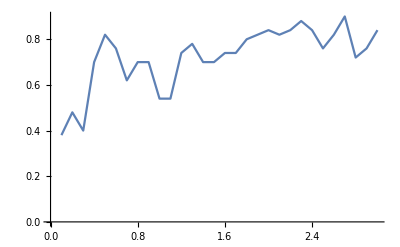

```mathematica
ListPlot[%29,Joined->True]
```

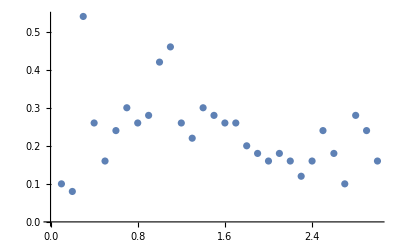

```mathematica
ListPlot[%26,Joined->False]
```

```mathematica
Table[{τ,ϕ[τ]},{τ,Range[0.1,3,0.1]}]
```

{{0.1,11/25},{0.2,19/50},{0.3,3/5},{0.4,17/25},{0.5,18/25},{0.6,19/25},{0.7,3/5},{0.8,17/25},{0.9,39/50},{1.,9/10},{1.1,41/50},{1.2,43/50},{1.3,22/25},{1.4,43/50},{1.5,41/50},{1.6,9/10},{1.7,47/50},{1.8,24/25},{1.9,24/25},{2.,9/10},{2.1,9/10},{2.2,47/50},{2.3,23/25},{2.4,1},{2.5,47/50},{2.6,23/25},{2.7,47/50},{2.8,47/50},{2.9,49/50},{3.,24/25}}

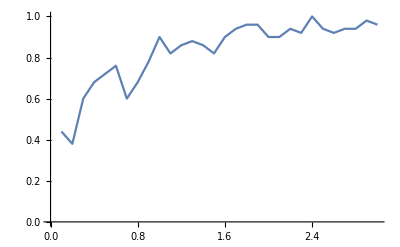

```mathematica
ListPlot[%36,Joined->True]
```

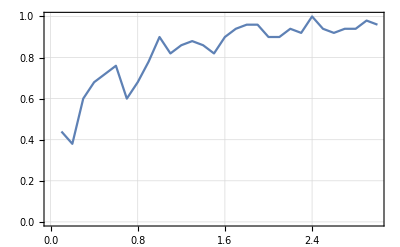

```mathematica
ListPlot[%36,PlotTheme->"Detailed",Joined->True]
```

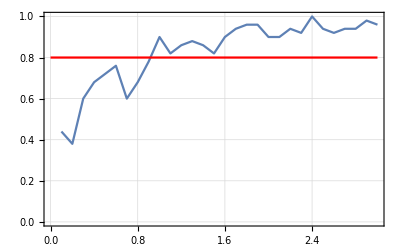

```mathematica
Show[%39,Plot[y=0.8,{y,0,3},PlotStyle->Red]]
```

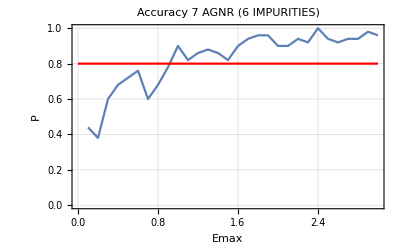

```mathematica
Show[%40,FrameLabel->{{HoldForm[P],None},{HoldForm[Emax],None}},PlotLabel->HoldForm[Accuracy 7 AGNR (6 IMPURITIES)],LabelStyle->{GrayLevel[0]}]
```